```mathematica
(* ΥΠΟΛΟΓΙΣΜΟΣ ΙΔΙΟΤΙΜΩΝ ΕΝΕΡΓΕΙΑΣ ΔΕΣΜΙΩΝ ΚΑΤΑΣΤΑΣΕΩΝ ΟΡΘΟΓΩΝΙΟΥ ΦΡΕΑΤΟΣ ΔΥΝΑΜΙΚΟΥ *)
```

```mathematica
(* ΑΡΙΘΜΗΤΙΚΗ ΜΕΘΟΔΟΣ *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* ΟΡΙΣΜΟΣ ΣΤΑΘΕΡΩΝ, 1 ΓΙΑ ΑΤΟΜΙΚΑ ΚΑΙ 2 ΓΙΑ ΠΥΡΗΝΙΚΑ ΣΥΣΤΗΜΑΤΑ *)
```

```mathematica
ic=1;   
Which[ ic==1, {c=26.247 , ctime=6.586*10^(-16)},
        ic==2, {c=0.0482, ctime=6.586*10^(-22)}     ]; 
v0=300;  L=0.2;
Print["ic=",ic,"  c=",c,"  ctime=",ctime,"  v0=",v0,"  L=",L];
```

ic=1  c=26.247  ctime=6.586×10^-16  v0=300  L=0.2

ic=1  c=26.247  ctime=6.586×10^-16  v0=300  L=0.2

ic=1  c=26.247  ctime=6.586×10^-16  v0=300  L=0.2

«1 more identical outputs»

```mathematica
(* PLOT ΤΟΥ ΟΡΘΟΓΩΝΙΟΥ ΦΡΕΑΤΟΣ ΔΥΝΑΜΙΚΟΥ *)
```

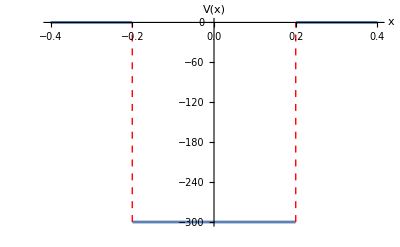

```mathematica
lineStyle={Thick,Red,Dashed};
line1=Line[{{-0.2,-300},{-0.2,0}}];
line2=Line[{{0.2,-300},{0.2,0}}];
 v[x_]:=Which[  Abs[x]≤L, -v0 ,
                            Abs[x] >L, 0 ];
figPot= Plot[ v[x], {x, -2 L, 2 L},
PlotStyle-> AbsoluteThickness[2],
AxesStyle -> AbsoluteThickness[1], AxesLabel->{"x","V(x)"},
Epilog->{Directive[lineStyle],line1,line2}   ]
```

```mathematica
(* ΟΙ ΣΧΕΣΕΙΣ ΠΟΥ ΔΙΝΟΥΝ ΤΙΣ ΔΕΣΜΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΓΙΑ ΤΙΣ ΑΡΤΙΕΣ ΚΑΙ ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΕΙΝΑΙ ΟΙ ΕΞΗΣ:
Sqrt[c*(ex+v0)]*Tan[Sqrt[c*(ex+v0)]*L]=Sqrt[-c*ex] (ΑΡΤΙΕΣ)
Sqrt[c*(ex+v0)]*Cot[Sqrt[c*(ex+v0)]*L]=-Sqrt[-c*ex] (ΠΕΡΙΤΤΕΣ)*)
```

Set::write: Tag Times in (5.12318 √(300+e x)) Tan[1.02464 √(300+e x)] is Protected.

Set::write: Tag Times in (5.12318 √(300+e x)) Cot[1.02464 √(300+e x)] is Protected.

```mathematica
(* Ο ΜΕΓΙΣΤΟΣ ΑΡΙΘΜΟΣ ΤΩΝ ΔΕΣΜΙΩΝ ΚΑΤΑΣΤΑΣΕΩΝ ΟΡΙΖΕΤΑΙ ΑΠΟ ΤΗΝ ΕΝΤΟΛΗ Ceiling *)
```

```mathematica
NmaxEven=Ceiling[ L*Sqrt[c*v0]/Pi ]; Nmax=2*NmaxEven-1;
energy=Table[Null,{20}];
```

```mathematica
(* ΑΡΧΙΚΑ ΟΡΙΖΟΥΜΕ ΤΑ ΔΙΑΣΤΗΜΑΤΑ ΟΠΟΥ ΘΑ ΨΑΞΟΥΜΕ. ΜΕΣΑ ΣΕ ΜΙΑ Do loop, ΒΡΙΣΚΟΥΜΕ ΤΙΣ ΔΕΣΜΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ ΜΕ ΤΗΝ ΕΝΤΟΛΗ FindRoot, ΕΝΩ ΜΕ ΤΟ If ΚΑΝΟΥΜΕ ΕΛΕΓΧΟ ΑΝ ΠΡΟΚΕΙΤΑΙ ΓΙΑ ΑΡΤΙΕΣ Η ΠΕΡΙΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ, ΩΣΤΕ ΝΑ ΕΠΑΛΗΘΕΥΣΟΥΜΕ ΤΟ ΑΠΟΤΕΛΕΣΜΑ. Η ΧΡΗΣΗ ΤΟΥ CHOP ΕΓΙΝΕ ΓΙΑ ΝΑ ΜΗΔΕΝΙΣΟΥΜΕ ΤΥΧΟΝ ΜΙΓΑΔΙΚΑ ΑΠΟΤΕΛΕΣΜΑΤΑ *)
```

```mathematica
Do[{  emin=-v0+ n^2*Pi^2/(4*c*L^2),
    emax=-v0+ (n+1)^2*Pi^2/(4*c*L^2),
If[EvenQ[n],
en=FindRoot[ Sqrt[c*(e+v0)]*Sin[Sqrt[c*(e+v0)]*L]==
                     Sqrt[-c*e]*Cos[Sqrt[c*(e+v0)]*L], {e,emin,emax}  ],
en=FindRoot[ Sqrt[c*(e+v0)]*Cos[Sqrt[c*(e+v0)]*L]==
                  - Sqrt[-c*e]*Sin[Sqrt[c*(e+v0)]*L], {e,emin,emax}   ]   
  ],
energy[[n]]=e/.en//Chop, 
ex=energy[[n]] ,
If[EvenQ[n],
    test=Sqrt[c*(ex+v0)]*Tan[Sqrt[c*(ex+v0)]*L]-Sqrt[-c*ex] ,
    test=Sqrt[c*(ex+v0)]*Cot[Sqrt[c*(ex+v0)]*L]+Sqrt[-c*ex]   
 ],
 Clear[e, en,ex],
 Print["Bound State Energy[",n, "]=",energy[[n]],"  test=",test   ] },
 {n,0,Nmax} ];
```

Bound State Energy[0]=-297.894  test=8.3844×10^-13

Bound State Energy[1]=-291.58  test=-1.9611×10^-12

Bound State Energy[2]=-281.067  test=-1.42109×10^-13

Bound State Energy[3]=-266.372  test=-6.6791×10^-13

Bound State Energy[4]=-247.524  test=1.13687×10^-13

Bound State Energy[5]=-224.562  test=-1.27898×10^-13

Bound State Energy[6]=-197.544  test=2.98428×10^-13

Bound State Energy[7]=-166.559  test=1.13687×10^-13

Bound State Energy[8]=-131.748  test=-4.9738×10^-14

Bound State Energy[9]=-93.3642  test=5.68434×10^-14

Bound State Energy[10]=-51.9626  test=-1.27898×10^-13

Bound State Energy[11]=-9.6594  test=-9.23706×10^-14

```mathematica
(* PLOT *)
```

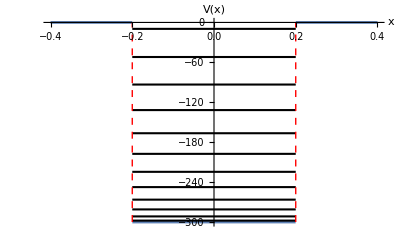

```mathematica
figBE=Graphics[ {  AbsoluteThickness[1.5],
Table[
Line[{ {-L,energy[[n]]},{L,energy[[n]]} }
      ],{n,0,Nmax}]           }];
Show[figPot,figBE,PlotRange->All]
```

```mathematica
(* ΕΥΡΕΣΗ ΑΡΤΙΩΝ ΚΑΙ ΠΕΡΙΤΤΩΝ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΕΩΝ *)
```

```mathematica
(* ΟΡΙΣΜΟΣ γ ΚΑΙ k (1.50) *)
```

```mathematica
g[e_]:=Sqrt[-c*e]; 
k[e_]:=Sqrt[c*(e+v0)];
```

```mathematica
(* ΟΡΙΣΜΟΣ Α2 (1.54) ΚΑΙ Β2 (1.57) *)
```

```mathematica
a2[e_]:= Exp[-g[e]*L]/Cos[k[e]*L];
b2[e_]:=- Exp[-g[e]*L]/Sin[k[e]*L];
```

```mathematica
(* ΑΡΤΙΑ *)
```

```mathematica
wf1even[e_,x_]:= Which[ x<=-L,  Exp[g[e]*x]  ,
                                   Abs[x]<=L,   a2[e]*Cos[k[e]*x],
                                             x>=L,  Exp[-g[e]*x ]  ];
normeven[e_]:=Sqrt[2* NIntegrate[wf1even[e,x]^2, {x,-5*L, 0} ]]; 
wfeven[e_,x_]:= wf1even[e,x]/normeven[e] ;
```

```mathematica
(* ΠΕΡΙΤΤΗ *)
```

```mathematica
wf1odd[e_,x_]:= Which[   x<=-L,  Exp[g[e]*x ]  ,
                                   Abs[x]<=L,   b2[e]*Sin[k[e]*x] ,
                                            x >=L, - Exp[-g[e]*x ]   ];
normodd[e_]:=Sqrt[2*NIntegrate[wf1odd[e,x]^2, {x,-5*L, 0}]]; 
wfodd[e_,x_]:= wf1odd[e,x]/normodd[e] ;
```

```mathematica
(*(α)*)
```

```mathematica
mxeven=Simplify[Integrate[x*wfeven[e,x]^2,{x,-5*L, 0} ]];
mxodd=Simplify[Integrate[x*wfodd[e,x]^2,{x,-5*L, 0} ]];
mx2even=Simplify[Integrate[(x^2)*wfeven[e,x]^2,{x,-5*L, 0} ]];
mx2odd=Simplify[Integrate[(x^2)*wfodd[e,x]^2,{x,-5*L, 0} ]];
aveven=Sqrt[mx2even-mxeven^2];
avodd=Sqrt[mx2odd-mxodd^2];
Print["ΟΙ ΑΒΕΒΑΙΟΤΗΤΕΣ ΘΕΣΗΣ ΤΩΝ ΠΕΡΙΤΩΝ ΚΑΙ ΤΩΝ ΑΡΤΙΩΝ ΚΑΤΑΣΤΑΣΕΩΝ ΘΑ ΕΙΝΑΙ " , N[aveven] ," " , N[avodd],"ΑΝΤΙΣΤΟΙΧΑ"];
```

```mathematica
(*(β)*)
```

```mathematica
x0=0;
dx=0.1*L;
k0=30;
t=0;
f[x_]:=Sqrt[(1/Sqrt[2*Pi]*dx)]*Exp[-(x-x0)^2/(4*dx^2)];
y[x_]:=f[x,t]*Exp[I*k0*x];
psi[x_,t_]:=y[x]*Exp[-I*ex*t/ℏ];
mx=Simplify[Integrate[x*psi[x,t]^2,{x,-L,L}]];
mx2=Simplify[Integrate[(x^2)*psi[x,t]^2,{x,-L,L}]];
av=Sqrt[mx2-mx^2];
```

```mathematica
Print["Η  ΧΡΟΝΙΚΗ ΕΞΕΛΙΞΗ ΤΟΥ ΜΕΤΡΟΥ ΤΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ ΚΑΙ ΤΗΣ ΑΒΕΒΑΙΟΤΗΤΑΣΤΗΣ ΘΕΣΗΣ ΕΙΝΑΙ","    " ,psi[x,t],"  &  " , av,"ΑΝΤΙΣΤΟΙΧΑ"];
```

Η  ΧΡΟΝΙΚΗ ΕΞΕΛΙΞΗ ΤΟΥ ΜΕΤΡΟΥ ΤΗΣ ΚΥΜΑΤΟΣΥΝΑΡΤΗΣΗΣ ΚΑΙ ΤΗΣ ΑΒΕΒΑΙΟΤΗΤΑΣΤΗΣ ΘΕΣΗΣ ΕΙΝΑΙ    0.0893244 ⅇ^(30 ⅈ x-625. x^2)  &  0.+0.000185055 ⅈΑΝΤΙΣΤΟΙΧΑ

```mathematica
(*(γ)*)
```

```mathematica
(*ΘΑ ΤΑ ΒΑΛΩ ΟΛΑ ΜΕΣΑ ΣΕ ΜΙΑ ΛΟΥΠΑ DO*)
```